Problem 10.3.9

#### n=20

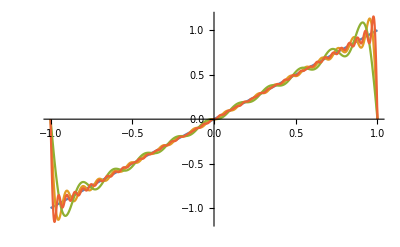

```mathematica
Plot[{Piecewise[{{x, -1≤x<1}, {x-2, 1≤x<2}}], Sum[(-2*Cos[m*Pi]/(m*Pi))*Sin[m*Pi*x], {m, 1, 20}], Sum[(-2*Cos[m*Pi]/(m*Pi))*Sin[m*Pi*x], {m, 1, 10}], Sum[(-2*Cos[m*Pi]/(m*Pi))*Sin[m*Pi*x], {m, 1, 40}]}, {x,-1, 1}]
```

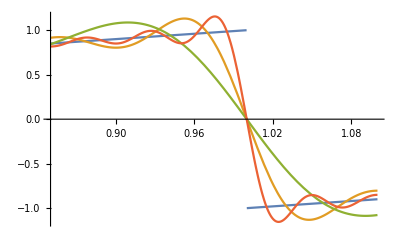

```mathematica
Plot[{Piecewise[{{x, -1≤x<1}, {x-2, 1≤x<2}}], Sum[(-2*Cos[m*Pi]/(m*Pi))*Sin[m*Pi*x], {m, 1, 20}], Sum[(-2*Cos[m*Pi]/(m*Pi))*Sin[m*Pi*x], {m, 1, 10}], Sum[(-2*Cos[m*Pi]/(m*Pi))*Sin[m*Pi*x], {m, 1, 40}]}, {x,0.85, 1.1}]
```

```mathematica
f[x_]:=x
```

```mathematica
g[x_]:=Sum[(-2*Cos[m*Pi]/(m*Pi))*Sin[m*Pi*x], {m, 1, 20}]
```

```mathematica
h[x_]:=Sum[(-2*Cos[m*Pi]/(m*Pi))*Sin[m*Pi*x], {m, 1, 10}]
```

```mathematica
j[x_]:=Sum[(-2*Cos[m*Pi]/(m*Pi))*Sin[m*Pi*x], {m, 1, 40}]
```

```mathematica
{f[1]-g[1], f[1]-h[1], f[1]-j[1]}
```

{1,1,1}

```mathematica
{f[0]-g[0], f[0]-h[0], f[0]-j[0]}
```

{0,0,0}

```mathematica
{f[-1]-g[-1], f[-1]-h[-1], f[-1]-j[-1]}
```

{-1,-1,-1}

#### part c

```mathematica
k[x_]:=0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 21}]
```

```mathematica
f[1]-k[1]
```

0.990795

#### Problem 10.4.24

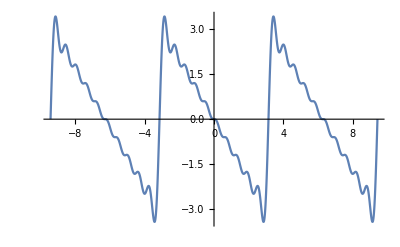

```mathematica
Plot[Sum[(2/n)*Cos[n*Pi]*Sin[n*x], {n,1,10}], {x, -3*Pi, 3*Pi}]
```